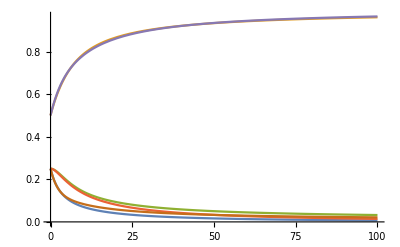

NDSolve::deqn: Equation or list of equations expected instead of 0.25 in the first argument ….

```mathematica
n = 3;
T1 = Table[i,{i,n}];
b;

t = Table[Subscript[r, i],{i,n}];
males= Table[Subscript[m, i],{i,n}];
females = Table[Subscript[f, i],{i,n}];
denom = Total[males];

dm = Table[0,{i,n}];
df = Table[0,{i,n}];

For[i = 1, i < n+1, i++,
dm[[i]] =(b/denom)*Sum[males[[x]]*females[[y]]*t[[y]] Boole[(x+ y)/2 == i],{x,1,n},{y,1,n}]
];

For[i = 1, i <n +1, i++,
dm[[i]] = dm[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*t[[y]] Boole[Floor[(x+ y)/2] == i && (x+y)/2 ≠ Floor[(x+ y)/2]],{x,1,n},{y,1,n}]
]

For[i = 1, i <n +1, i++,
dm[[i]] = dm[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*t[[y]] Boole[Ceiling[(x+ y)/2] == i && (x+y)/2 ≠ Ceiling[(x+ y)/2]],{x,1,n},{y,1,n}]
]

For[i = 1, i < n+1, i++,
df[[i]] =(b/denom)*Sum[males[[x]]*females[[y]]*(1-t[[y]]) Boole[(x+ y)/2 == i],{x,1,n},{y,1,n}]
];

For[i = 1, i <n +1, i++,
df[[i]] = df[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*(1-t[[y]]) Boole[Floor[(x+ y)/2] == i && (x+y)/2 ≠ Floor[(x+ y)/2]],{x,1,n},{y,1,n}]
]

For[i = 1, i <n +1, i++,
df[[i]] = df[[i]] + (b/denom)*(1/2)*Sum[males[[x]]*females[[y]]*(1-t[[y]]) Boole[Ceiling[(x+ y)/2] == i && (x+y)/2 ≠ Ceiling[(x+ y)/2]],{x,1,n},{y,1,n}]
]

all = FullSimplify[Total[dm]];
denom2 = Total[females /. {Subscript[f, p_]:> Subscript[y, p]}];

f[p_] := Subscript[y, p] *denom
h[q_] := If[q < n, Subscript[x, q]*denom, (1-Sum[Subscript[x, i],{i,1,n-1}])*denom]
g[z_] := If[z <n, Subscript[q, z]*denom2 , (1-Sum[Subscript[q, i],{i,1,n-1}])*denom2];
e[z_] := If[z <n, Subscript[q, z], (1-Sum[Subscript[q, i],{i,1,n-1}])];

dm2 = Table[0,{i,n}];
df2 = Table[0,{i,n}];

For[ i = 1,i < n+1,i++,
dm2[[i]] = FullSimplify[(dm[[i]])/denom -(males[[i]]/denom^2)*all  /. {Subscript[f, q_] :>f[q], Subscript[m, p_] :> h[p] }];
]

For[ i = 1,i < n+1,i++,
df2[[i]] = FullSimplify[(df[[i]])/denom -(females[[i]]/denom^2)*all/. {Subscript[f, q_] :>f[q], Subscript[m, p_] :> h[p] }];
]

df3 = Table[0,{i,n}];
femall = FullSimplify[Total[df2]];

For[i = 1,i<n+1,i++,
df3[[i]] = FullSimplify[df2[[i]]/denom2 - (Subscript[y, i]/denom2^2)*femall /. {Subscript[y, z_] :> g[z]}]
]

For[i = 1, i<n+1,i++,
dm2[[i]] = FullSimplify[dm2[[i]] /. {Subscript[y, z_] :> e[z]}]]


f2[a_] := If[a < n, Subscript[x, a][s], (1-Sum[Subscript[x, i][s],{i,1,n-1}])];
f3[c_] := If[c <n, Subscript[q, c][s], (1-Sum[Subscript[q, c][s],{i,1,n-1}])];

sys = Table[j,{j,2n-2}];

For [i = 1,i < n, i++,
sys[[i]] = Subscript[x, i]'[s]== (dm2[[i]] /. {Subscript[x, a_] :> f2[a], Subscript[q, c_] :> f3[c]})]

For[i = 1,i<n,i++,
sys[[i+n-1]] = Subscript[q, i]'[s] == (df3[[i]] /. {Subscript[x, a_] :> f2[a], Subscript[q, c_] :> f3[c]})
]

MaleSym = Table[Subscript[x, i],{i,n-1}];
FemaleSym = Table[Subscript[q, i],{i,n-1}];

b = 1;
Subscript[r, 1] = 0.25;
Subscript[r, 2] = 0.5;
Subscript[r, 3] = 0.75;
tmax = 100;

sol := NDSolve[{sys,Subscript[x, 1][0] == 0.25, Subscript[x, 2][0] == 0.5, Subscript[q, 1][0] ==0.25, Subscript[q, 2][0] == 0.5},{MaleSym,FemaleSym},{s,0,tmax}];

c1 := sol[[1]][[1]][[2]][[1]]
c2 := sol[[1]][[1]][[2]][[2]]
d1 := sol[[1]][[2]][[2]][[1]]
d2 := sol[[1]][[2]][[2]][[2]]
Plot[{c1[x],c2[x],1-c1[x]-c2[x], d1[x], d2[x], 1-d1[x]-d2[x]},{x,0,tmax}]
```